### Ilustração do Teorema do Limite Central - Distribuição comum Uniforme (0, 1)

a) Simulação de uma amostra de rep=1000 médias padronizadas de n v.a. i.i.d. a Uniforme(0,1), com n igual a

b) Comparação do histograma da amostra de médias padronizadas de n=2  v.a. i.i.d. a Uniforme(0,1) com a f.d.p. da normal-padrão

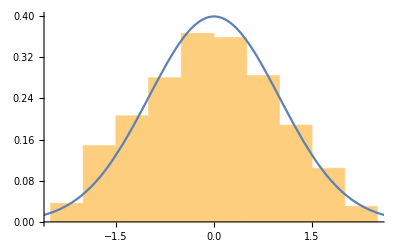

c) Comparação da f.d. empírica da amostra de médias padronizadas de n=2  v.a. i.i.d. a Uniforme(0,1) (azul) com a f.d. da normal-padrão (laranja)

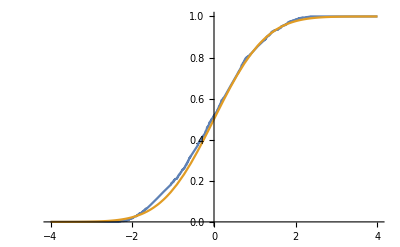

```mathematica
Print["a) Simulação de uma amostra de rep=1000 médias padronizadas de n v.a. i.i.d. a Uniforme(0,1), com n igual a"]
n=Input["Introduza o valor de n"];
rep=1000;

dist=UniformDistribution[{0,1}];
i=0;
vecmean={};
While[i<rep,
vecmean=Append[vecmean,Mean[RandomVariate[dist,n]]];i++]
stvecmean=(vecmean-Mean[dist])/(√(Variance[dist]/n));
Print["b) Comparação do histograma da amostra de médias padronizadas de n=",n,"  v.a. i.i.d. a Uniforme(0,1) com a f.d.p. da normal-padrão"]
Show[Histogram[stvecmean,Automatic,"PDF"],
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]]

Print["c) Comparação da f.d. empírica da amostra de médias padronizadas de n=",n,"  v.a. i.i.d. a Uniforme(0,1) (azul) com a f.d. da normal-padrão (laranja)"]
F[x_]=1/rep×∑_(j=1)^rep If[stvecmean[[j]]≤x,1,0];
Plot[{F[x],CDF[NormalDistribution[0,1],x]},{x,-4,4}]
```

### Ilustração do Teorema do Limite Central - Distribuição comum Exponencial (λ=1)

a) Simulação de uma amostra de rep=1000 médias padronizadas de n v.a. i.i.d. a Exponencial(1), com n igual a

b) Comparação do histograma da amostra de médias padronizadas de n=31 v.a. i.i.d. a Exponencial(1) com a f.d.p. da normal-padrão

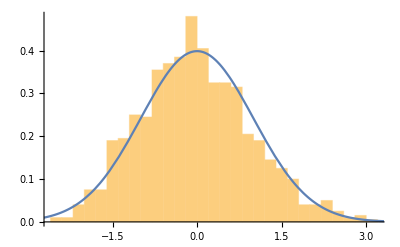

c) Comparação da f.d. empírica da amostra de médias padronizadas de n=31 v.a. i.i.d. a Exponencial(1) (azul) com a f.d. da normal-padrão (laranja)

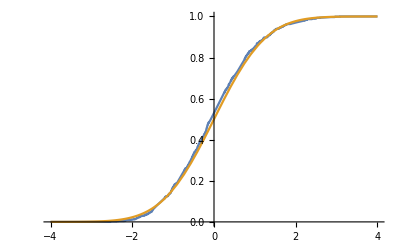

```mathematica
Print["a) Simulação de uma amostra de rep=1000 médias padronizadas de n v.a. i.i.d. a Exponencial(1), com n igual a"]
n=Input["Introduza o valor de n"];
rep=1000;

dist=ExponentialDistribution[1];
i=0;
vecmean={};
While[i<rep,
vecmean=Append[vecmean,Mean[RandomVariate[dist,n]]];i++]
stvecmean=(vecmean-Mean[dist])/(√(Variance[dist]/n));

Print["b) Comparação do histograma da amostra de médias padronizadas de n=",n," v.a. i.i.d. a Exponencial(1) com a f.d.p. da normal-padrão"]
Show[Histogram[stvecmean,Automatic,"PDF"],
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]]

Print["c) Comparação da f.d. empírica da amostra de médias padronizadas de n=",n," v.a. i.i.d. a Exponencial(1) (azul) com a f.d. da normal-padrão (laranja)"]
F[x_]=1/rep×∑_(j=1)^rep If[stvecmean[[j]]≤x,1,0];
Plot[{F[x],CDF[NormalDistribution[0,1],x]},{x,-4,4}]
```

### Ilustração do Teorema do Limite Central - Distribuição comum Bernoulli (p)

a) Simulação de uma amostra de rep=1000 somas padronizadas de n v.a. i.i.d. a Bernoulli(p), com n e p iguais a

25

0.3

b) Comparação do histograma da amostra de somas padronizadas de n=25 v.a. i.i.d. a Bernoulli(p=0.3) com a f.d.p. da normal-padrão

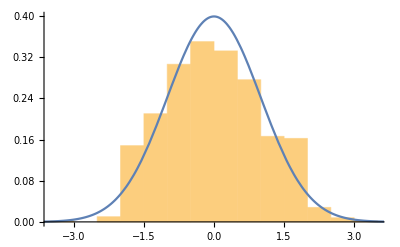

c) Comparação da f.d. empírica da amostra de somas padronizadas de n=25 v.a. i.i.d. a Bernoulli(p=0.3) 
(azul) com a f.d. da normal-padrão (laranja)

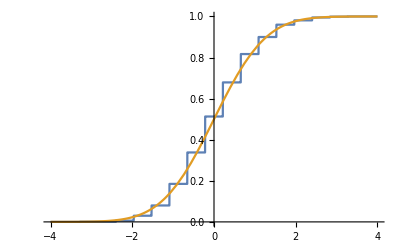

```mathematica
Print["a) Simulação de uma amostra de rep=1000 somas padronizadas de n v.a. i.i.d. a Bernoulli(p), com n e p iguais a"]
n=Input["Introduza o valor de n"]
p=Input["Introduza o valor de p"]
rep=1000;

dist=BernoulliDistribution[p];
i=0;
vecmean={};
While[i<rep,
vecmean=Append[vecmean,n×Mean[RandomVariate[dist,n]]];i++]
stvecmean=(vecmean-n×Mean[dist])/(√(n×Variance[dist]));

Print["b) Comparação do histograma da amostra de somas padronizadas de n=",n," v.a. i.i.d. a Bernoulli(p=",p,") com a f.d.p. da normal-padrão"]
Show[Histogram[stvecmean,Automatic,"PDF"],
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]]

Print["c) Comparação da f.d. empírica da amostra de somas padronizadas de n=",n," v.a. i.i.d. a Bernoulli(p=",p,") 
(azul) com a f.d. da normal-padrão (laranja)"]
F[x_]=1/rep×∑_(j=1)^rep If[stvecmean[[j]]≤x,1,0];
Plot[{F[x],CDF[NormalDistribution[0,1],x]},{x,-4,4}]
```

### Ilustração do Teorema do Limite Central - Distribuição comum Poisson (λ=1)

a) Simulação de uma amostra de rep=1000 somas padronizadas de n v.a. i.i.d. a Poisson(λ=1), com n igual a

41

b) Comparação do histograma da amostra de somas padronizadas de n=41 v.a. i.i.d. a Poisson(λ=1) com a f.d.p. da normal-padrão

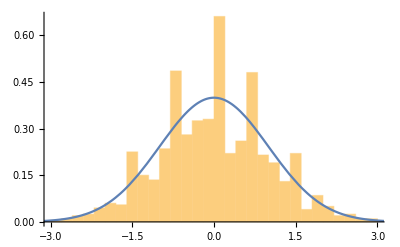

c) Comparação da f.d. empírica da amostra de somas padronizadas de n=41 v.a. i.i.d. a Poisson(λ=1) (azul) com a f.d. da normal-padrão (laranja)

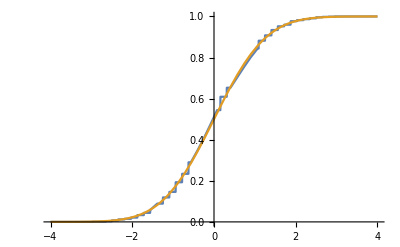

```mathematica
Print["a) Simulação de uma amostra de rep=1000 somas padronizadas de n v.a. i.i.d. a Poisson(λ=1), com n igual a"]
n=Input["Introduza o valor de n"]
rep=1000;

dist=PoissonDistribution[1];
i=0;
vecmean={};
While[i<rep,
vecmean=Append[vecmean,Mean[RandomVariate[dist,n]]];i++]
stvecmean=(vecmean-Mean[dist])/(√(Variance[dist]/n));

Print["b) Comparação do histograma da amostra de somas padronizadas de n=",n," v.a. i.i.d. a Poisson(λ=1) com a f.d.p. da normal-padrão"]
Show[Histogram[stvecmean,Automatic,"PDF"],
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]]

Print["c) Comparação da f.d. empírica da amostra de somas padronizadas de n=",n," v.a. i.i.d. a Poisson(λ=1) (azul) com a f.d. da normal-padrão (laranja)"]
F[x_]=1/rep×∑_(j=1)^rep If[stvecmean[[j]]≤x,1,0];
Plot[{F[x],CDF[NormalDistribution[0,1],x]},{x,-4,4}]
```